```mathematica
proof=ResourceFunction["FindWolframModelProof"][{{1,2}}<->{{1,2},{2,4},{2,3},{3,5}},{{x,y}}<->{{x,y},{y,z}}]
```

ProofObject[WolframModelLogic,1⊕2==(1⊕2)⊙((2⊕4)⊙((2⊕3)⊙(3⊕5))),∀_{x,y,z}x⊕y==(x⊕y)⊙(y⊕z)&&∀_{a,b,c}a⊙(b⊙c)==(a⊙b)⊙c&&∀_{a,b}a⊙b==b⊙a,{{Axiom,1}→<|Statement→x1⊙x2==x2⊙x1,Proof→<||>|>,{Axiom,2}→<|Statement→x1⊙(x2⊙x3)==(x1⊙x2)⊙x3,Proof→<||>|>,{Axiom,3}→<|Statement→(x1⊕x2)⊙(x2⊕x3)==x1⊕x2,Proof→<||>|>,{Hypothesis,1}→<|Statement→(1⊕2)⊙((2⊕4)⊙((2⊕3)⊙(3⊕5)))==1⊕2,Proof→<||>|>,{SubstitutionLemma,1}→<|Statement→((2⊕4)⊙((2⊕3)⊙(3⊕5)))⊙(1⊕2)==1⊕2,Proof→<|Input→{Hypothesis,1},Position→1,Construct→{Axiom,1},Orientation→{-1,1},Rule→x1_⊙x2_→x2⊙x1,OutputExpression→((2⊕4)⊙((2⊕3)⊙(3⊕5)))⊙(1⊕2)==1⊕2|>|>,{SubstitutionLemma,2}→<|Statement→(2⊕4)⊙(((2⊕3)⊙(3⊕5))⊙(1⊕2))==1⊕2,Proof→<|Input→{SubstitutionLemma,1},Position→1,Construct→{Axiom,2},Orientation→-1,Rule→(x1_⊙x2_)⊙x3_→x1⊙(x2⊙x3),OutputExpression→(2⊕4)⊙(((2⊕3)⊙(3⊕5))⊙(1⊕2))==1⊕2|>|>,{SubstitutionLemma,3}→<|Statement→(((2⊕3)⊙(3⊕5))⊙(1⊕2))⊙(2⊕4)==1⊕2,Proof→<|Input→{SubstitutionLemma,2},Position→1,Construct→{Axiom,1},Orientation→{-1,1},Rule→x1_⊙x2_→x2⊙x1,OutputExpression→(((2⊕3)⊙(3⊕5))⊙(1⊕2))⊙(2⊕4)==1⊕2|>|>,{SubstitutionLemma,4}→<|Statement→((1⊕2)⊙((2⊕3)⊙(3⊕5)))⊙(2⊕4)==1⊕2,Proof→<|Input→{SubstitutionLemma,3},Position→{1,1},Construct→{Axiom,1},Orientation→{-1,1},Rule→x1_⊙x2_→x2⊙x1,OutputExpression→((1⊕2)⊙((2⊕3)⊙(3⊕5)))⊙(2⊕4)==1⊕2|>|>,{SubstitutionLemma,5}→<|Statement→((1⊕2)⊙(2⊕3))⊙(2⊕4)==1⊕2,Proof→<|Input→{SubstitutionLemma,4},Position→{1,1,2},Construct→{Axiom,3},Orientation→1,Rule→(x1_⊕x2_)⊙(x2_⊕x3_)→x1⊕x2,OutputExpression→((1⊕2)⊙(2⊕3))⊙(2⊕4)==1⊕2|>|>,{SubstitutionLemma,6}→<|Statement→(1⊕2)⊙(2⊕4)==1⊕2,Proof→<|Input→{SubstitutionLemma,5},Position→{1,1},Construct→{Axiom,3},Orientation→1,Rule→(x1_⊕x2_)⊙(x2_⊕x3_)→x1⊕x2,OutputExpression→(1⊕2)⊙(2⊕4)==1⊕2|>|>,{Conclusion,1}→<|Statement→True,Proof→<|Input→{SubstitutionLemma,6},Position→1,Construct→{Axiom,3},Orientation→1,Rule→(x1_⊕x2_)⊙(x2_⊕x3_)→x1⊕x2,OutputExpression→True|>|>}]

```mathematica
proof["ProofDataset"]
```

ProofObject[WolframModelLogic,1⊕2==(1⊕2)⊙((2⊕4)⊙((2⊕3)⊙(3⊕5))),∀_{x,y,z}x⊕y==(x⊕y)⊙(y⊕z)&&∀_{a,b,c}a⊙(b⊙c)==(a⊙b)⊙c&&∀_{a,b}a⊙b==b⊙a,{{Axiom,1}→<|Statement→x1⊙x2==x2⊙x1,Proof→<||>|>,{Axiom,2}→<|Statement→x1⊙(x2⊙x3)==(x1⊙x2)⊙x3,Proof→<||>|>,{Axiom,3}→<|Statement→(x1⊕x2)⊙(x2⊕x3)==x1⊕x2,Proof→<||>|>,{Hypothesis,1}→<|Statement→(1⊕2)⊙((2⊕4)⊙((2⊕3)⊙(3⊕5)))==1⊕2,Proof→<||>|>,{SubstitutionLemma,1}→<|Statement→((2⊕4)⊙((2⊕3)⊙(3⊕5)))⊙(1⊕2)==1⊕2,Proof→<|Input→{Hypothesis,1},Position→1,Construct→{Axiom,1},Orientation→{-1,1},Rule→x1_⊙x2_→x2⊙x1,OutputExpression→((2⊕4)⊙((2⊕3)⊙(3⊕5)))⊙(1⊕2)==1⊕2|>|>,{SubstitutionLemma,2}→<|Statement→(2⊕4)⊙(((2⊕3)⊙(3⊕5))⊙(1⊕2))==1⊕2,Proof→<|Input→{SubstitutionLemma,1},Position→1,Construct→{Axiom,2},Orientation→-1,Rule→(x1_⊙x2_)⊙x3_→x1⊙(x2⊙x3),OutputExpression→(2⊕4)⊙(((2⊕3)⊙(3⊕5))⊙(1⊕2))==1⊕2|>|>,{SubstitutionLemma,3}→<|Statement→(((2⊕3)⊙(3⊕5))⊙(1⊕2))⊙(2⊕4)==1⊕2,Proof→<|Input→{SubstitutionLemma,2},Position→1,Construct→{Axiom,1},Orientation→{-1,1},Rule→x1_⊙x2_→x2⊙x1,OutputExpression→(((2⊕3)⊙(3⊕5))⊙(1⊕2))⊙(2⊕4)==1⊕2|>|>,{SubstitutionLemma,4}→<|Statement→((1⊕2)⊙((2⊕3)⊙(3⊕5)))⊙(2⊕4)==1⊕2,Proof→<|Input→{SubstitutionLemma,3},Position→{1,1},Construct→{Axiom,1},Orientation→{-1,1},Rule→x1_⊙x2_→x2⊙x1,OutputExpression→((1⊕2)⊙((2⊕3)⊙(3⊕5)))⊙(2⊕4)==1⊕2|>|>,{SubstitutionLemma,5}→<|Statement→((1⊕2)⊙(2⊕3))⊙(2⊕4)==1⊕2,Proof→<|Input→{SubstitutionLemma,4},Position→{1,1,2},Construct→{Axiom,3},Orientation→1,Rule→(x1_⊕x2_)⊙(x2_⊕x3_)→x1⊕x2,OutputExpression→((1⊕2)⊙(2⊕3))⊙(2⊕4)==1⊕2|>|>,{SubstitutionLemma,6}→<|Statement→(1⊕2)⊙(2⊕4)==1⊕2,Proof→<|Input→{SubstitutionLemma,5},Position→{1,1},Construct→{Axiom,3},Orientation→1,Rule→(x1_⊕x2_)⊙(x2_⊕x3_)→x1⊕x2,OutputExpression→(1⊕2)⊙(2⊕4)==1⊕2|>|>,{Conclusion,1}→<|Statement→True,Proof→<|Input→{SubstitutionLemma,6},Position→1,Construct→{Axiom,3},Orientation→1,Rule→(x1_⊕x2_)⊙(x2_⊕x3_)→x1⊕x2,OutputExpression→True|>|>}][ProofDataset]

```mathematica
proof=ResourceFunction["FindWolframModelProof"][{{1,2}}<->{{1,2},{2,4},{2,3},{3,5}},{{x,y}}<->{{x,y},{y,z}}];
```

```mathematica
proof["ProofGraph"]
```

ProofObject[WolframModelLogic,1⊕2==(1⊕2)⊙((2⊕4)⊙((2⊕3)⊙(3⊕5))),∀_{x,y,z}x⊕y==(x⊕y)⊙(y⊕z)&&∀_{a,b,c}a⊙(b⊙c)==(a⊙b)⊙c&&∀_{a,b}a⊙b==b⊙a,{{Axiom,1}→<|Statement→x1⊙x2==x2⊙x1,Proof→<||>|>,{Axiom,2}→<|Statement→x1⊙(x2⊙x3)==(x1⊙x2)⊙x3,Proof→<||>|>,{Axiom,3}→<|Statement→(x1⊕x2)⊙(x2⊕x3)==x1⊕x2,Proof→<||>|>,{Hypothesis,1}→<|Statement→(1⊕2)⊙((2⊕4)⊙((2⊕3)⊙(3⊕5)))==1⊕2,Proof→<||>|>,{SubstitutionLemma,1}→<|Statement→((2⊕4)⊙((2⊕3)⊙(3⊕5)))⊙(1⊕2)==1⊕2,Proof→<|Input→{Hypothesis,1},Position→1,Construct→{Axiom,1},Orientation→{-1,1},Rule→x1_⊙x2_→x2⊙x1,OutputExpression→((2⊕4)⊙((2⊕3)⊙(3⊕5)))⊙(1⊕2)==1⊕2|>|>,{SubstitutionLemma,2}→<|Statement→(2⊕4)⊙(((2⊕3)⊙(3⊕5))⊙(1⊕2))==1⊕2,Proof→<|Input→{SubstitutionLemma,1},Position→1,Construct→{Axiom,2},Orientation→-1,Rule→(x1_⊙x2_)⊙x3_→x1⊙(x2⊙x3),OutputExpression→(2⊕4)⊙(((2⊕3)⊙(3⊕5))⊙(1⊕2))==1⊕2|>|>,{SubstitutionLemma,3}→<|Statement→(((2⊕3)⊙(3⊕5))⊙(1⊕2))⊙(2⊕4)==1⊕2,Proof→<|Input→{SubstitutionLemma,2},Position→1,Construct→{Axiom,1},Orientation→{-1,1},Rule→x1_⊙x2_→x2⊙x1,OutputExpression→(((2⊕3)⊙(3⊕5))⊙(1⊕2))⊙(2⊕4)==1⊕2|>|>,{SubstitutionLemma,4}→<|Statement→((1⊕2)⊙((2⊕3)⊙(3⊕5)))⊙(2⊕4)==1⊕2,Proof→<|Input→{SubstitutionLemma,3},Position→{1,1},Construct→{Axiom,1},Orientation→{-1,1},Rule→x1_⊙x2_→x2⊙x1,OutputExpression→((1⊕2)⊙((2⊕3)⊙(3⊕5)))⊙(2⊕4)==1⊕2|>|>,{SubstitutionLemma,5}→<|Statement→((1⊕2)⊙(2⊕3))⊙(2⊕4)==1⊕2,Proof→<|Input→{SubstitutionLemma,4},Position→{1,1,2},Construct→{Axiom,3},Orientation→1,Rule→(x1_⊕x2_)⊙(x2_⊕x3_)→x1⊕x2,OutputExpression→((1⊕2)⊙(2⊕3))⊙(2⊕4)==1⊕2|>|>,{SubstitutionLemma,6}→<|Statement→(1⊕2)⊙(2⊕4)==1⊕2,Proof→<|Input→{SubstitutionLemma,5},Position→{1,1},Construct→{Axiom,3},Orientation→1,Rule→(x1_⊕x2_)⊙(x2_⊕x3_)→x1⊕x2,OutputExpression→(1⊕2)⊙(2⊕4)==1⊕2|>|>,{Conclusion,1}→<|Statement→True,Proof→<|Input→{SubstitutionLemma,6},Position→1,Construct→{Axiom,3},Orientation→1,Rule→(x1_⊕x2_)⊙(x2_⊕x3_)→x1⊕x2,OutputExpression→True|>|>}][ProofGraph]

### DFA to Hypergraph

```mathematica
alphabetGraphHelper[n_]:= If[n ==0, {{1,1},{1,2}},If[n==1,{{1,2},{2,1}}, Module[{x},x = Last[#][[1]]&[alphabetGraphHelper[n-1]]; Join[Drop[#,-1],{{x,x+1},{x+1,1}}]&
[alphabetGraphHelper[n-1]]]]]
```

```mathematica
alphabetGraph[n_]:=If[n==0,{{1,1},{1,2}},Append[alphabetGraphHelper[n],{1,n+2}]]
```

```mathematica
concatenategraphs[g1_,g2_]:= graphToHypergraph[Join[{Max[VertexList[g1]]<->Max[VertexList[#]]},#]]&[EdgeList[GraphDisjointUnion[g1,g2]]]
```

```mathematica
concatenategraphs[cyclicgraph[2],cyclicgraph[3]]
```

GraphDisjointUnion::graph: A graph object is expected at position 1 in GraphDisjointUnion[{{0,1},{1,2},{2,0}},{{0,1},{1,2},{2,3},{3,0}}].

EdgeList::graph: A graph object is expected at position 1 in EdgeList[GraphDisjointUnion[{{0,1},{1,2},{2,0}},{{0,1},{1,2},{2,3},{3,0}}]].

VertexList::graph: A graph object is expected at position 1 in VertexList[{{0,1},{1,2},{2,0}}].

VertexList::graph: A graph object is expected at position 1 in VertexList[EdgeList[GraphDisjointUnion[{{0,1},{1,2},{2,0}},{{0,1},{1,2},{2,3},{3,0}}]]].

Join::heads: Heads List and EdgeList at positions 1 and 2 are expected to be the same.

Join[{VertexList[{{0,1},{1,2},{2,0}}]<->VertexList[EdgeList[GraphDisjointUnion[{{0,1},{1,2},{2,0}},{{0,1},{1,2},{2,3},{3,0}}]]]},EdgeList[GraphDisjointUnion[{{0,1},{1,2},{2,0}},{{0,1},{1,2},{2,3},{3,0}}]]]

Combines graph g1 and g2 where g1 has a vertex with vertex number x at x and g2 iwoth y.

```mathematica
GraphDisjointUnion[{{8,9},{4,5}},{{2,3}}]//EdgeList
```

{8<->9,4<->5,11<->12}

g1, g2 are lists of lists.

```mathematica
graphToHypergraph[g_]:= g /. (x_Integer<->y_Integer -> {x,y})
```

```mathematica
stateGraph[n_]:= Join[Table[{i,i},{i,1,n+3}],Table[{i,i+1},{i,1,n+3-1}],{{n+3,1}}]
```

```mathematica
initialWordToHypergraphHelper[word_List,acc_]:=If[word == {},acc,initialWordToHypergraphHelper[Drop[word,1],concatenategraphs[acc, alphabetGraph[word[[1]]]] ]]
```

```mathematica
Clear[concatenategraphs]
```

```mathematica
cyclicgrph[2]
```

{{0,1},{1,2},{2,0}}

```mathematica
stateGraph[0]
```

{{1,1},{2,2},{3,3},{1,2},{2,3},{3,1}}

```mathematica
concatenategraphs[cyclicgraph[2], stateGraph[2]]
```

{{3,8},{1,1},{2,2},{3,3},{1,2},{2,3},{3,1},{4,4},{5,5},{6,6},{7,7},{8,8},{4,5},{5,6},{6,7},{7,8},{8,4}}

```mathematica
initialWordToHypergraph[word_List]:= initialWordToHypergraphHelper[Drop[word,1],concatenategraphs[stateGraph[0],alphabetGraph[word[[1]]]]]
```

```mathematica
DFARule[{stateI_, alphabet_, stateF_}]:= ((#->  ReplaceAll[stateGraph[stateF],Join[Table[i->Max[VertexList[#]]+i,{i,1,stateF + 3-1}],{stateF + 3 ->Max[VertexList[#]] }]])&)[concatenategraphs[stateGraph[stateI],alphabetGraph[alphabet]]]
```

```mathematica
DFAtoHypergraph[rules_List,word_]:= ResourceFunction["WolframModel"][Table[DFARule[i],{i,Map[Join[#[[1]],#[[2]]]&,(rules /. Rule->List)]}],initialWordToHypergraph[word],Length[word],"EventsStatesPlotsList"]
```

Converts to word without state. That’s cool!

```mathematica
HypergraphToWord[hypergraph_]:=
```

f(H) = w iff h(w) is isomorphic to H where h(w) is the hypergraph of word w without the 0 state.  So this is immediately not injective because we can just take a graph isomorphism of H. Hmm, gotta study algorithms on graphs. Finding a subgraph. we can start with the one “end” or something..this is nice! WEell, there are a few tests. For examples, the

```mathematica
Graph[initialWordToHypergraph[{0,1,2,3,4,5,5,2,2,3}]]
```

-Graphics-

```mathematica
VertexDegree[%645]
```

{4,4,5,3,3,3,2,3,3,2,2,3,3,2,2,2,3,3,2,2,2,2,3,3,2,2,2,2,2,3,3,2,2,2,2,2,3,3,2,2,3,3,2,2,3,3,2,2,2,2}

We can find subgraphs. This function is an injective partial computable function that takes in a hypergraph Hand gives you a word w iff the hypergraph of word w is isomorphic to the

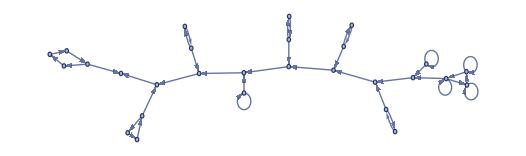

```mathematica
ResourceFunction["WolframModelPlot"][initialWordToHypergraph[{0,1,1,1,0,1,2,3}]]
```

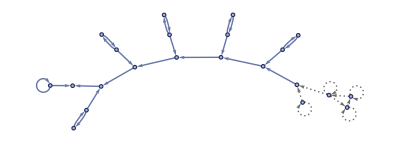
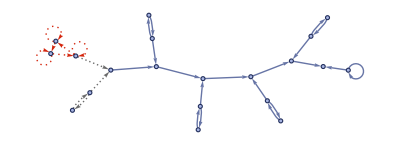
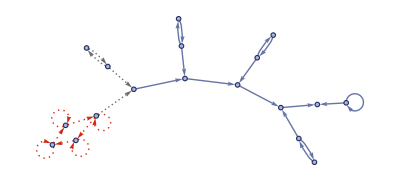
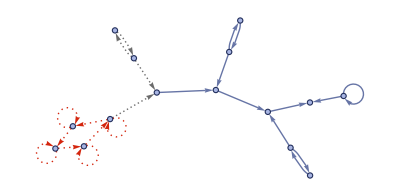
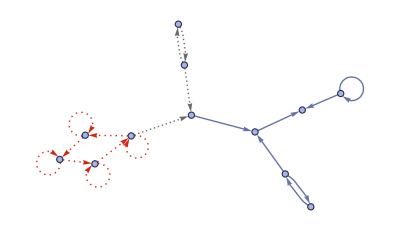
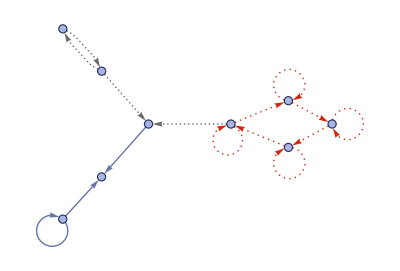
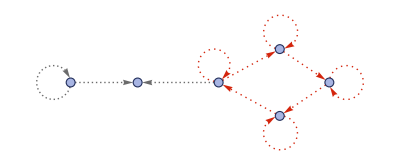
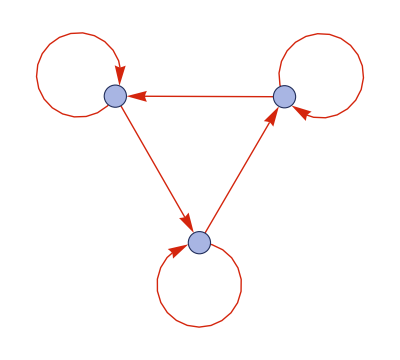

```mathematica
DFAtoHypergraph[{{0,0}->{0},{0,1}->{1},{1,0}->{0},{1,1}->{1}},{0,1,1,1,1,1,0}]
```

```mathematica
NFAtoHypergraph[rules_List,word_]:= 
ResourceFunction["MultiwaySystem"]["WolframModel"->ResourceFunction["CanonicalWolframModelRule"][Table[DFARule[i],{i,Map[Join[#[[1]],#[[2]]]&,(rules /. Rule->List)]}]],{initialWordToHypergraph[word]},Length[word],"StatesGraph",VertexSize->1]
```

```mathematica
NFAtoHypergraph[{{0,0}->{0},{0,0}->{1},{0,1}->{1},{0,1}->{2},{1,0}->{1},{1,0}->{2},{1,1}->{0},{1,1}->{1},{2,0}->{0},{2,0}->{1},{2,1}->{1},{2,1}->{0}},{0}]
```

-Graphics-

Done,

The problem is that is finds a separate subgraph to apply the rule to,,,it doesn’t care about the output. So the mutliwaya system applies all the non-overlapping rules at the same time. BUt here there is on;y once choice.  I see the problem now. Ok, got it.